```mathematica
Quit[]
```

# Ansatz for the GAs from EH Formula

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
```

## Fitting Functions

### Eisenstein-Hu Fitting Formula

```mathematica
(* All the formulas are extracted from EH97I[9709112 v1] paper,unless stated. *)
Θ=Solve[2.7*x==2.728]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)
h=0.67810; (* Reduced Hubble constant *)
(* See Eq. (11) *)
a1[ωm_]:=(46.9ωm)^0.670 (1+(32.1 ωm)^-0.532)
a2[ωm_]:=(12.0 ωm)^0.424 (1+(45.0 ωm)^-0.582) 
αc[ωb_,ωm_]:=a1[ωm]^(-ωb/ωm)*a2[ωm]^(-(ωb/ωm)^3)
(* See Eq. (12) *)
b1[ωm_] := 0.944 (1+(458 ωm)^-0.708)^-1 
b2[ωm_]:=(0.395 ωm)^-0.0266 
βc[ωb_,ωm_]:=(1+b1[ωm](((ωm - ωb)/ωm)^b2[ωm]-1))^-1 
(* Redshift at drag epoch -> See Eq. (4) *)
b1d[ωm_]:=0.313 ωm^-0.419 (1 + 0.607 ωm^0.674) 
b2d[ωm_]:=0.238 ωm^0.223 
zd[ωb_,ωm_]:=1291*ωm^0.251/(1 + 0.659 ωm^0.828)(1 + b1d[ωm] ωb^b2d[ωm]) 
zeq[ωm_]:=2.5*10^4 ωm*Θ^-4 (* Redshift at equilibrium epoch -> See Eq. (2) *)
keq[ωm_]:=7.46*10^-2 ωm*Θ^-2  (* scale at equilibrium epoch -> See Eq. (3) *)
q[k_,ωm_] := k/(13.41 keq[ωm])  (* See Eq. (10) *)
R[z_,ωb_]:=31.5*ωb*Θ^-4*(z/10^3)^-1  (* Baryon-Photon ratio -> See Eq. (5) *)
yEH[z_,ωm_]:=(1+zeq[ωm])/(1+z) (* Useful variable for calculations in LS limit -> See Eq.(8.20) in Dodelson 2 *)
(* Sub-horizon solution of the Mezsaros' eq. -> See Eq. (8.63) in Dodelson 2 *)
G[z_,ωm_]:=yEH[z, ωm] (-6 √(1+yEH[z,ωm])+(2+3yEH[z,ωm])Log[(√(1 + yEH[z, ωm])+1)/(√(1 + yEH[z, ωm])-1)]) 
(* Silk damping scale -> See Eq. (7) *)
ksilk[ωb_,ωm_]:=1.6 ωb^0.52*ωm^0.73(1+(10.4 ωm)^-0.95) (* [(Mpc^-1)]*)
βnode[ωm_]:=8.41*ωm^0.435 (* Shifting of nodes parameter -> See Eq. (23) *)
(* Sound horizon at drag epoch -> See Eq. (6) *)
s[ωb_,ωm_]:=2/(3 keq[ωm])√(6/R[zeq[ωm],ωb])Log[(√(1+R[zd[ωb,ωm],ωb])+√(R[zd[ωb,ωm],ωb]+R[zeq[ωm],ωb]))/(1+√R[zeq[ωm],ωb])]
st[k_,ωb_,ωm_]:=s[ωb,ωm]/((1+(βnode[ωm]/(k*s[ωb, ωm]))^3)^(1/3)) (* Shifting of oscillations nodes -> See Eq. (22) *)
(* Amplitude of small scale contributions -> See Eq. (14) *)
αb[ωb_,ωm_]:=2.07*keq[ωm]*s[ωb,ωm] (1+R[zd[ωb,ωm],ωb])^(-3/4)G[yEH[zd[ωb,ωm],ωm], ωm] 

(* Small scale contributions -> See Eq. (24) *)
βb[ωb_,ωm_]:=0.5+ωb/ωm+(3-2 ωb/ωm) √((17.2 ωm)^2+1)
f[k_,ωb_,ωm_]:=1/(1 + ((k*s[ωb, ωm])/5.4)^4) (* See Eq (18) *)
Cf[k_,ωb_,ωm_]:=14.2/αc[ωb,ωm]+386/(1 + 69.9*q[k,ωm]^1.08) (* See Eq. (20) *)
Cfαc1[k_,ωb_,ωm_]:=14.2 + 386/(1 + 69.9*q[k,ωm]^1.08) (* Cf with αc = 1*)
(* See Eq. (19) *)
T0[k_,ωb_,ωm_]:=Log[ⅇ + 1.8*βc[ωb,ωm]*q[k,ωm]]/(Log[ⅇ+1.8 βc[ωb,ωm]*q[k,ωm]]+Cf[k,ωb,ωm]*q[k,ωm]^2)
(* See Eqs. (19) and (20) in EH97: T0(k, 1, βc) means αc = 1 in Eq. (20) *)
T01[k_,ωb_,ωm_]:=Log[ⅇ+1.8*βc[ωb,ωm]*q[k,ωm]]/(Log[ⅇ + 1.8 βc[ωb,ωm]*q[k,ωm]]+Cfαc1[k,ωb,ωm]*q[k,ωm]^2)
(* See Eq. (19) in EH97: T0(k, 1, 1) means αc = 1 in Eq. (20) and βc = 1 in Eq. (19) *)
T011[k_,ωb_,ωm_]:=Log[ⅇ+1.8*q[k,ωm]]/(Log[E+1.8*q[k,ωm]]+Cfαc1[k,ωb,ωm]*q[k,ωm]^2)
(* Transfer function for CDM -> See Eq. (17) *)
TcEH[k_,ωb_,ωm_]:=f[k,ωb,ωm]*T01[k,ωb,ωm]+(1-f[k,ωb,ωm])T0[k,ωb,ωm]
(* Transfer function for baryons -> See Eq. (21) *)
TbEH[k_,ωb_,ωm_]:=(T011[k, ωb, ωm]/(1+((k*s[ωb,ωm])/5.2)^2)+αb[ωb,ωm]/(1 + (βb[ωb,ωm]/(k*s[ωb,ωm]))^3)ⅇ^(-(k/ksilk[ωb,ωm])^1.4))Sin[k*st[k,ωb,ωm]]/(k*st[k,ωb,ωm])
(* Transfer function for CDM + baryons -> See Eq. (16) *)
TEH[k_,ωb_,ωm_] := (ωm - ωb)/ωm TcEH[k,ωb,ωm]+ωb/ωm TbEH[k,ωb,ωm]
```

### Eisenstein-Hu Fitting Formula: No-Wiggles

```mathematica
sh[ωb_,ωm_]:=(44.5*Log[9.83/ωm])/(√(1+10 ωb^(3/4))); (* Mpc *)
αΓ[ωb_,ωm_]:=1-0.328*Log[431*ωm]*ωb/ωm+0.38*Log[22.3*ωm]*(ωb/ωm)^2
Γeff[k_,ωb_,ωm_]:=ωm/h(αΓ[ωb,ωm]+(1-αΓ[ωb,ωm])/(1+(0.43*k*sh[ωb,ωm])^4));
qeff[k_,ωb_,ωm_]:=k/h*Θ^2/Γeff[k,ωb,ωm]; (* k in h/Mpc *)
L0eff[k_,ωb_,ωm_]:=Log[2ⅇ+1.8*qeff[k,ωb,ωm]];
C0eff[k_,ωb_,ωm_]:=14.2+731/(1+62.5*qeff[k,ωb,ωm]);
TEHnw[k_,ωb_,ωm_]:=L0eff[k,ωb,ωm]/(L0eff[k,ωb,ωm]+C0eff[k,ωb,ωm]*qeff[k,ωb,ωm]^2)
```

## Searching for Wiggles in the EH Formula

## Parts of T_EH: T_c and T_b

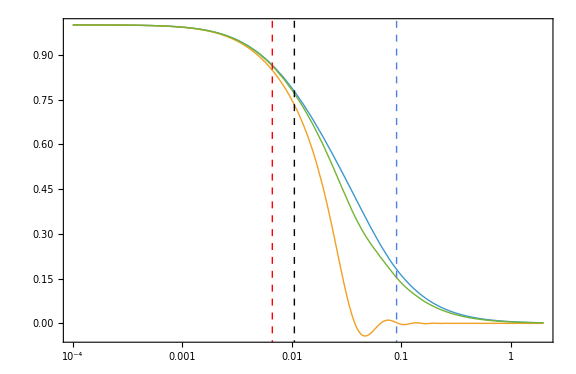

```mathematica
(* Each part of the EH formula -> Subscript[T, b] provide a suppression *)
LogLinearPlot[{TcEH[k*h,ωb,ωm],TbEH[k*h,ωb,ωm],TEH[k*h,ωb,ωm]}/.{ωb->0.0224,ωm->0.1448}//Evaluate,{k,10^-4,2},PlotRange->All,PlotStyle->{Directive[Thick],Directive[Thick],Directive[Thick],Directive[Thick,Dashed]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"k \\, [h / \\text{Mpc}]","\\text{Transfer Functions}"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.8] &)/@Style["T_c"],
(MaTeX[#, Magnification -> 1.8] &)/@Style["T_b"],
(MaTeX[#, Magnification -> 1.8] &)/@Style["T_\\text{EH}"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,5},LegendMarkerSize->{35},LegendFunction->Frame],{0.12,0.27}],AspectRatio->0.65,Epilog->{{(*Sound Horizon*)Dashed,Thick,Red,Line[{{Log[1/s[0.0224,0.1448]],-2},{Log[1/s[0.0224,0.1448]],2}}]},{(*keq*)Dashed,Thick,Black,Line[{{Log[keq[0.1448]],-2},{Log[keq[0.1448]],2}}]},{(*ksilk*)Dashed,Thick,RGBColor[0.3,0.5,0.9],Line[{{Log[ksilk[0.0224,0.1448]],-2},{Log[ksilk[0.0224,0.1448]],2}}]}},ImageSize->Large]
```

## Wiggles in T_b

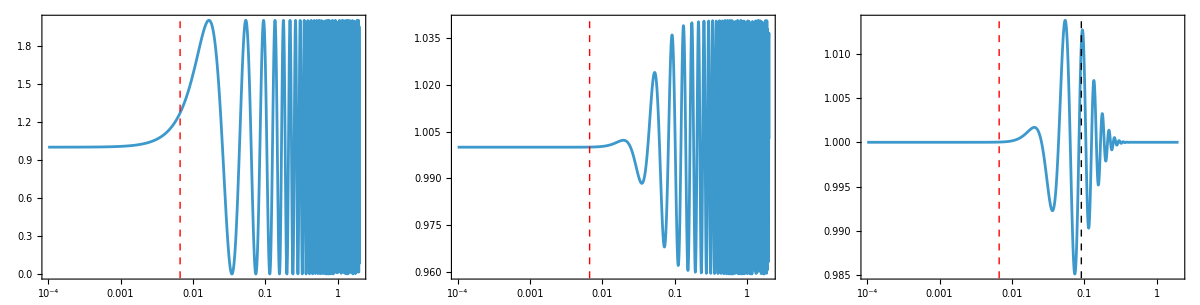

```mathematica
(* Effects of some terms in Subscript[T, b] *)
(*  Oscillations below the sound horizon (ks > 1): Sin(ks) *)
LogLinearPlot[1+Sin[k*st[k,ωb,ωm]]/.{ωb->0.0224,ωm->0.1448}//Evaluate,{k,10^-4,2},PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.2]&)/@{"k \\, [h / \\text{Mpc}]"},BaseStyle->{FontFamily->"Times",FontSize->10},Epilog->{(*Sound Horizon*)Dashed,Thick,Red,Line[{{Log[1/s[0.0224,0.1448]],-2},{Log[1/s[0.0224,0.1448]],2}}]},AspectRatio->0.65];
(*  Suppression of amplitude: 
	Subscript[α, b]: Suppresion factor -> specifies the small-scale asymptotic contribution to the acoustic oscillations
	Subscript[β, b]: Cut-off scale for the suppression *)
LogLinearPlot[1+(αb[ωb,ωm]/(1 + (βb[ωb,ωm]/(k*s[ωb,ωm]))^3))*Sin[k*st[k,ωb,ωm]]/.{ωb->0.0214,ωm->0.13}//Evaluate,{k,10^-4,2},PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.2]&)/@{"k \\, [h / \\text{Mpc}]"},BaseStyle->{FontFamily->"Times",FontSize->10},Epilog->{(*Sound Horizon*)Dashed,Thick,Red,Line[{{Log[1/s[0.0224,0.1448]],-2},{Log[1/s[0.0224,0.1448]],2}}]},AspectRatio->0.65];
(* ) Exponential damping due to photon diffusion (Silk damping): 
	ⅇ^(-k/Subscript[k, silk]): Subscript[k, Silk] is the diffusion scale
   Subscript[β, node]: Moves the nodes to higher k *)
LogLinearPlot[1+αb[ωb,ωm]/(1 + (βb[ωb,ωm]/(k*s[ωb,ωm]))^3)*ⅇ^(-(k/ksilk[ωb,ωm])^1.4)*Sin[k*s[ωb,ωm]/((1+(βnode[ωm]/(k s[ωb,ωm]))^3)^(1/3))]/.{ωb->0.0224,ωm->0.1448}//Evaluate,{k,10^-4,2},PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.2]&)/@{"k \\, [h / \\text{Mpc}]"},BaseStyle->{FontFamily->"Times",FontSize->10},Epilog->{{(*Sound Horizon*)Dashed,Thick,Red,Line[{{Log[1/s[0.0224,0.1448]],-2},{Log[1/s[0.0224,0.1448]],2}}]},{(*ksilk*)Dashed,Thick,Black,Line[{{Log[ksilk[0.0224,0.1448]],-2},{Log[ksilk[0.0224,0.1448]],2}}]}},AspectRatio->0.65];
GraphicsRow[{%%%,%%,%},ImageSize->Full,Frame->All]
```

```mathematica
(* This suggests the following formulation: 
	Subscript[T, w](k, Subscript[ω, b], Subscript[ω, m])= 1 + Subscript[f, amp](k, Subscript[ω, b], Subscript[ω, m])*Subscript[f, silk](k, Subscript[ω, b], Subscript[ω, m])*Sin(Subscript[f, node](k, Subscript[ω, b], Subscript[ω, m])) *)
```

## Approximations to Relevant Terms in T_b

```mathematica
(* Sound horizon from GAs [arXiv:2106.00428]: *)
c1=0.00785436;c2=0.177084;c3=0.00912388;c4=0.618711;
c5=11.9611;c6=2.81343;c7=0.784719;
sGAs[ωb_,ωm_]:=1/(c1*ωb^c2+c3*ωm^c4+c5*ωb^c6*ωm^c7)
```

### Amplitude Function

```mathematica
(* Subscript[α, b] is a complicated function -> It can be highly simplified *)
?αb
αb[ωb,ωm]
```

(3.01141 √(ωm/ωb) (1+23989.3 ωm) Log[(√(1+(23.4133 ωb (1+0.659 ωm^0.828))/((1+(0.313 ωb^(0.238 ωm^0.223) (1+0.607 ωm^0.674))/ωm^0.419) ωm^0.251))+√((1.26 ωb)/ωm+(23.4133 ωb (1+0.659 ωm^0.828))/((1+(0.313 ωb^(0.238 ωm^0.223) (1+0.607 ωm^0.674))/ωm^0.419) ωm^0.251)))/(1+1.1225 √(ωb/ωm))] (-6 √(1+(1+23989.3 ωm)/(1+(1+23989.3 ωm)/(1+(1291 (1+(0.313 ωb^(0.238 ωm^0.223) (1+0.607 ωm^0.674))/ωm^0.419) ωm^0.251)/(1+0.659 ωm^0.828))))+(2+(3 (1+23989.3 ωm))/(1+(1+23989.3 ωm)/(1+(1291 (1+(0.313 ωb^(0.238 ωm^0.223) (1+0.607 ωm^0.674))/ωm^0.419) ωm^0.251)/(1+0.659 ωm^0.828)))) Log[(1+√(1+(1+23989.3 ωm)/(1+(1+23989.3 ωm)/(1+(1291 (1+(0.313 ωb^(0.238 ωm^0.223) (1+0.607 ωm^0.674))/ωm^0.419) ωm^0.251)/(1+0.659 ωm^0.828)))))/(-1+√(1+(1+23989.3 ωm)/(1+(1+23989.3 ωm)/(1+(1291 (1+(0.313 ωb^(0.238 ωm^0.223) (1+0.607 ωm^0.674))/ωm^0.419) ωm^0.251)/(1+0.659 ωm^0.828)))))]))/((1+(23.4133 ωb (1+0.659 ωm^0.828))/((1+(0.313 ωb^(0.238 ωm^0.223) (1+0.607 ωm^0.674))/ωm^0.419) ωm^0.251))^(3/4) (1+(1+23989.3 ωm)/(1+(1291 (1+(0.313 ωb^(0.238 ωm^0.223) (1+0.607 ωm^0.674))/ωm^0.419) ωm^0.251)/(1+0.659 ωm^0.828))))

```mathematica
(* Evaluate Subscript[α, b] in several points *)
SeedRandom[12345];
ωbvals=RandomReal[{0.0214,0.0234},100];
ωmvals=RandomReal[{0.13,0.15},100];
```

```mathematica
(* Ansatz for Subscript[α, b] *)
fαb[ωb_,ωm_,a_,b_,c_,d_]:=a+b*ωb^c+d*ωm
```

```mathematica
(* Fitness function *)
χ2αb[a_,b_,c_,d_]:=Mean[Table[Abs[αb[ωbvals[[i]],ωmvals[[i]]]-fαb[ωbvals[[i]],ωmvals[[i]],a,b,c,d]]/αb[ωbvals[[i]],ωmvals[[i]]]*100,{i,1,Length[ωbvals]}]]
```

```mathematica
(* Most probable parameters -> Very accurate: Acc ~ 0.02% *)
Paramsαb=NMinimize[χ2αb[a,b,c,d],{a,b,c,d},AccuracyGoal->100,Method->"RandomSearch"]
```

{0.0208993,{a→0.131173,b→-0.209954,c→0.157385,d→0.186002}}

```mathematica
(* Subscript[α, b] is basically a polynomial. *)
fαb[ωb,ωm,a,b,c,d]/.Paramsαb[[2]]
```

0.131173-0.209954 ωb^0.157385+0.186002 ωm

```mathematica
(* Subscript[β, b] is simple but it is possible to make it simpler *)
?βb
```

```mathematica
(* Ansatz for Subscript[β, b] -> Straight line *)
fβb[ωb_,ωm_,a_,b_,c_]:=a+b*ωb+c*ωm
```

```mathematica
(* Fitness function *)
χ2βb[a_,b_,c_]:=Mean[Table[Abs[βb[ωbvals[[i]],ωmvals[[i]]]-fβb[ωbvals[[i]],ωmvals[[i]],a,b,c]]/βb[ωbvals[[i]],ωmvals[[i]]]*100,{i,1,Length[ωbvals]}]]
```

```mathematica
(* Very accurate approximation: Acc ~ 0.007 *)
Paramsβb=NMinimize[χ2βb[a,b,c],{a,b,c},AccuracyGoal->100,Method->"RandomSearch"]
```

{0.00724822,{a→1.68668,b→-30.2817,c→47.4275}}

```mathematica
(* Simple functional form *)
fβb[ωb,ωm,a,b,c]/.Paramsβb[[2]]
```

1.68668-30.2817 ωb+47.4275 ωm

```mathematica
(* Simple ansatz for the amplitude function: *)
(* Subscript[f, amp](Subscript[ω, b], Subscript[ω, m]) ~ Paddé(k, Subscript[ω, b], Subscript[ω, m]) *)
OldAmpFunc[k_,ωb_,ωm_]:=αb[ωb,ωm]/(1 + (βb[ωb,ωm]/(k*s[ωb,ωm]))^3)
NewAmpFunc[k_,ωb_,ωm_]:=(fαb[ωb,ωm,a,b,c,d]/.Paramsαb[[2]])/(1+((fβb[ωb,ωm,a,b,c]/.Paramsβb[[2]])/(k*sGAs[ωb,ωm]))^3)
```

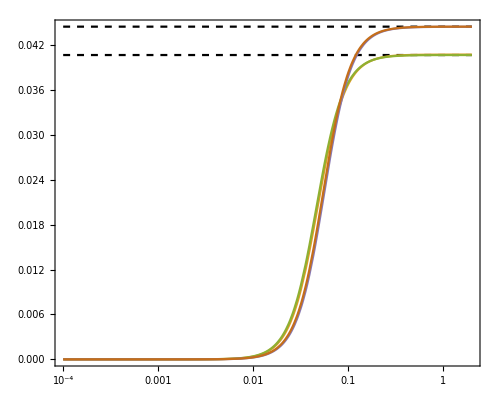

```mathematica
LogLinearPlot[{αb[0.0214,0.13],NewAmpFunc[k,0.0214,0.13],OldAmpFunc[k,0.0214,0.13],αb[0.0214,0.15],NewAmpFunc[k,0.0214,0.15],OldAmpFunc[k,0.0214,0.15]},{k,10^-4,2},PlotRange->All,PlotStyle->{Directive[Black,Dashed],"",""},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]"},BaseStyle->{FontFamily->"Times",FontSize->20},AspectRatio->0.8,ImageSize->500]
```

```mathematica
(* The new amplitude function is far simpler: *)
NewAmpFunc[k,ωb,ωm]//LeafCount
OldAmpFunc[k,ωb,ωm]//LeafCount
```

50

626

### Silk Damping Function

```mathematica
(* Subscript[k, silk] is already simple *)
?ksilk
```

```mathematica
kSilkData=Import["./Data/k_silk.dat","Data"][[2;;-1]](* {Subscript[ω, b],Subscript[ω, m],Subscript[k, Silk]} *)
```

{{0.0214,0.13,0.095562},{0.0214,0.137,0.0967217},{0.0214,0.143,0.0978565},{0.0214,0.15,0.0990408},{0.0221,0.13,0.0965639},{0.0221,0.137,0.0977357},{0.0221,0.143,0.0988823},{0.0221,0.15,0.100079},{0.0227,0.13,0.0974017},{0.0227,0.137,0.0985835},{0.0227,0.143,0.0997403},{0.0227,0.15,0.100947},{0.0234,0.13,0.0983529},{0.0234,0.137,0.0995458},{0.0234,0.143,0.100713},{0.0234,0.15,0.101932}}

```mathematica
kSilkEH[ωb_,ωm_]:=1.6 ωb^0.52*ωm^0.73(1+(10.4 ωm)^-0.95)
```

```mathematica
ωbvals={0.0214,0.0220666,0.0227333,0.0234};
ωmvals={0.13,0.13666,0.143333,0.15};
```

```mathematica
ωcvals=ωmvals-ωbvals
```

{0.1086,0.114593,0.1206,0.1266}

```mathematica
scales={46.492137,45.934698,45.402007,44.859123,46.009762,45.458136,44.931004,44.393717,45.614037,45.067206,44.544519,44.011887,45.172883,44.631531,44.114146,43.586668};
```

```mathematica
ksilkdata=(2π)/scales (* [1/Mpc] *)
```

{0.135145,0.136785,0.13839,0.140065,0.136562,0.138219,0.139841,0.141533,0.137747,0.139418,0.141054,0.142761,0.139092,0.140779,0.14243,0.144154}

```mathematica
(* Ansatz for Subscript[k, Silk]*)
fkSilk[ωb_,ωm_,a_,b_,c_,d_]:=a *ωb^b+c*ωm^d
```

```mathematica
(* Fitness function *)
χ2Silk[a_,b_,c_,d_]:=Mean[Table[Abs[kSilkData[[i,3]]-fkSilk[kSilkData[[i,1]],kSilkData[[i,2]],a,b,c,d]]/kSilkData[[i,3]]*100,{i,1,Length[kSilkData]} ]]
```

```mathematica
Paramsχ2Silk=NMinimize[χ2Silk[a,b,c,d],{a,b,c,d},AccuracyGoal->10,Method->"RandomSearch"]
```

{0.0305249,{a→0.373315,b→0.418692,c→0.195285,d→1.09568}}

```mathematica
Mean[Table[Abs[ksilkdata[[i]]-kSilkEH[kSilkData[[i,1]],kSilkData[[i,2]]]]/ksilkdata[[i]]*100,{i,1,Length[ksilkdata]} ]]
```

35.6938

```mathematica
a *ωb^b+c*ωm^d/.{a->0.3733148571907788,b->0.418692097487844,c->0.19528535966155064,d->1.0956810620791562}
```

0.373315 ωb^0.418692+0.195285 ωm^1.09568

### Nodes Function

```mathematica
?st
```

```mathematica
?βnode
```

```mathematica
(* We only replace s by Subscript[s, GA] and we get a far simpler expression *)
sGAs[ωb,ωm]/((1+(βnode[ωm]/(k*sGAs[ωb,ωm]))^3)^(1/3))//LeafCount
st[k,ωb,ωm]//LeafCount
```

57

253